Generate the sequence of notes with pitches 0, 4 and 7.

EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
Sound[{SoundNote[0],SoundNote[4],SoundNote[7]}]
```

Generate 2 seconds of playing middle A on a cello.

EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
Sound[SoundNote["A", 2, "Cello"]]
```

Generate a “riff” of notes from pitch 0 to pitch 48 in steps of 1, with each note lasting 0.05 seconds.

EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
Sound[Table[SoundNote[n, 0.05], {n, 0, 48}]]
```

Generate a sequence of notes going from pitch 12 down to 0 in steps of 1.

EXPECTED OUTPUT »

-Graphics- | ×

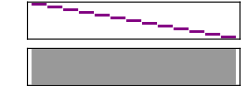

```mathematica
Sound[Table[SoundNote[n], {n, 12, 0,-1}]]
```

Generate a sequence of 5 notes starting with middle C, then successively going up by an octave at a time.

EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
Sound[Table[SoundNote[n], {n, 0, 48,12}]]
```

Generate a sequence of 10 notes on a trumpet with random pitches from 0 to 12 and duration 0.2 seconds.

SAMPLE EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
Sound[Table[SoundNote[RandomInteger[12], 0.2, "Trumpet"], {n, 10}]]
```

Generate a sequence of 10 notes with random pitches up to 12 and random durations up to 10 tenths of a second.

SAMPLE EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
Sound[Table[SoundNote[RandomInteger[12], 0.1 RandomInteger[10]], {n, 10}]]
```

Generate 0.1-second notes with pitches given by the digits of 2^31.

EXPECTED OUTPUT »

-Graphics- | ×

Create a sound from the letters in CABBAGE, each playing for 0.3 seconds sounding like a guitar.

EXPECTED OUTPUT »

-Graphics- | ×

Generate 0.1-second notes with pitches given by the letter numbers of the characters in “wolfram”.

EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
[ Click to enter code ]
```

Generate a sequence of three notes of 1 second of playing middle D on the cello, piano and guitar.

EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
[ Click to enter code ]
```

Generate a sequence of notes from pitch 0 to pitch 12, going up in steps of 3.

EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
[ Click to enter code ]
```

Generate a sequence of 5 notes starting with middle C, then successively going up by a perfect fifth (7 semitones) at a time.

EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
[ Click to enter code ]
```

Generate 0.02-second notes with pitches given by the lengths of the names of integers from 1 to 200.

EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
[ Click to enter code ]
```